```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/BHbook/math"];
```

## inflaton potential

### inflection

```mathematica
Delta[a_]=a^2/3(9/(2 a^2)-1)^(2/3);
bc[a_]=1-1/3 a^2+Delta[a];
```

```mathematica
Vinflection[x_]=x^2/12(6-4a x+3 x^2)/((1+b x^2)^2)/.{a->1,b->bc[1]-10^-4}//Simplify;
```

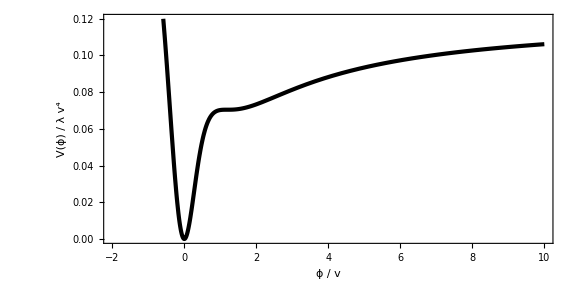

```mathematica
Plot[Vinflection[x],{x,-2,10},PlotRange->{0,0.12},PlotStyle->{Black,AbsoluteThickness[3]},FrameLabel->{Row[{ϕ," / ",v}],Row[{V[ϕ]," / ",λ v^4}]},AspectRatio->1/2]
```

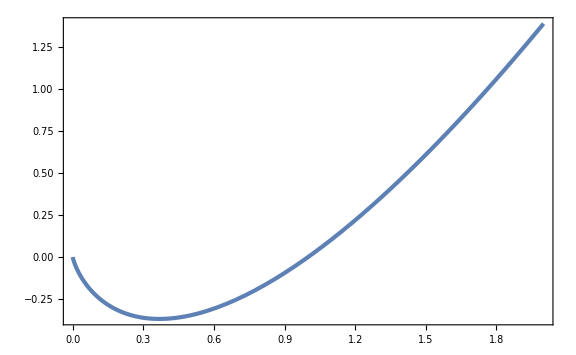

```mathematica
Plot[x Log[x],{x,0,2}]
```

```mathematica
Collect[Normal[Series[x^4(1+a Log[x]^2),{x,1,4}]],x,Simplify]
Collect[Normal[Series[(1+c(1+b Log[x])x^2)^2,{x,1,4}]],x,Simplify]
```

(11 a)/12-(14 a x)/3+(19 a x^2)/2-(26 a x^3)/3+(1+(35 a)/12) x^4

1+(11 b^2 c^2)/12+1/6 b c (1+3 c)-2/3 b c (2+(4+7 b) c) x+1/2 c (4+12 b c+19 b^2 c) x^2-2/3 b c (-2+(12+13 b) c) x^3+1/12 c (12 c+35 b^2 c+b (-2+50 c)) x^4

### multi-phase

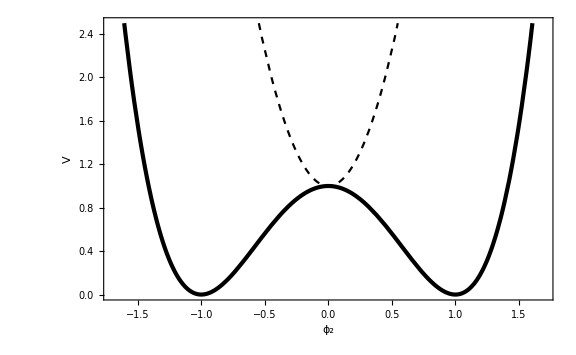

```mathematica
Plot[{(1-x^2)^2,1+5 x^2},{x,-1.7,1.7},PlotRange->{0,2.5},PlotStyle->{{Black,AbsoluteThickness[3]},{Black,Dashed}},FrameLabel->{Subscript[ϕ, 2],V},FrameTicks->None]
```

## q-param

```mathematica
zetaGx[x_,mu_]=mu Sin[x]/x//Simplify
```

(mu Sin[x])/x

```mathematica
zetabar[x_,mu_,fNL_]=zetaGx[x,mu]+3/5 fNL zetaGx[x,mu]^2//Simplify
```

(mu Sin[x] (5 x+3 fNL mu Sin[x]))/(5 x^2)

```mathematica
CompactC[x_,mu_,fNL_]=2/3(1-(1+x D[zetabar[x,mu,fNL], x])^2)//FullSimplify
```

2/3 (1-((5 x^2+mu (x Cos[x]-Sin[x]) (5 x+6 fNL mu Sin[x]))^2)/(25 x^4))

```mathematica
rmcond[x_,mu_,fNL_]=-(5 x^20)/mu(D[zetabar[x,mu,fNL], x]+x D[D[zetabar[x,mu,fNL], x], x])//Simplify
```

x^17 (-6 fNL mu+5 x^2 Cos[x]-6 fNL mu (-1+x^2) Cos[2 x]-5 x Sin[x]+5 x^3 Sin[x]+9 fNL mu x Sin[2 x])

```mathematica
rmcond2[x_,mu_,fNL_]=1/x(1+x D[zetabar[x,mu,fNL], x])//Simplify
```

(5 x^2-5 mu x Sin[x]-6 fNL mu^2 Sin[x]^2+mu x Cos[x] (5 x+6 fNL mu Sin[x]))/(5 x^3)

```mathematica
rmcond2minList=Flatten[ParallelTable[{fNL,mu,FindMinimum[{rmcond2[x,mu,fNL],0<x<5},{x,3}][[1]]},{fNL,-4.1,4.1,10^-2},{mu,0.5,1.1,10^-2}],1];//AbsoluteTiming
```

$Aborted

```mathematica
Export["rmcond2min_fNL.dat",rmcond2minList];
```

```mathematica
rmcond2minList=Import["rmcond2min_fNL.dat"]//ToExpression;
```

```mathematica
ListContourPlot[rmcond2minList]
```

-Graphics-

```mathematica
rmcond2minint[fNL_,mu_]=Interpolation[rmcond2minList][fNL,mu];
```

```mathematica
mu2List=Table[{fNL,mu/.FindRoot[rmcond2minint[fNL,mu]==0,{mu,0.8}]},{fNL,-4.1,4.1,10^-2}];
```

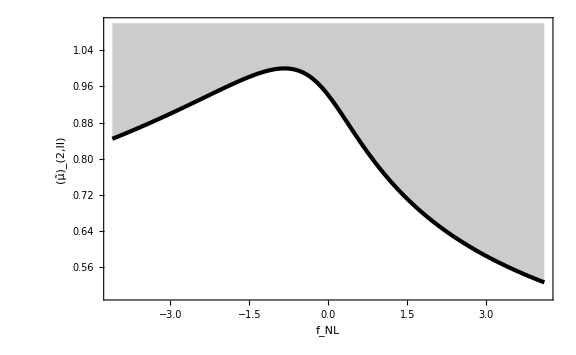

```mathematica
ListPlot[mu2List,PlotStyle->{AbsoluteThickness[3],Black},Filling->Top,FrameLabel->{Subscript[f, NL],Subscript[OverTilde[μ], 2,II]},PlotRange->{0.5,1.1}]
```

```mathematica
mu2int[fNL_]=Interpolation[mu2List][fNL];
```

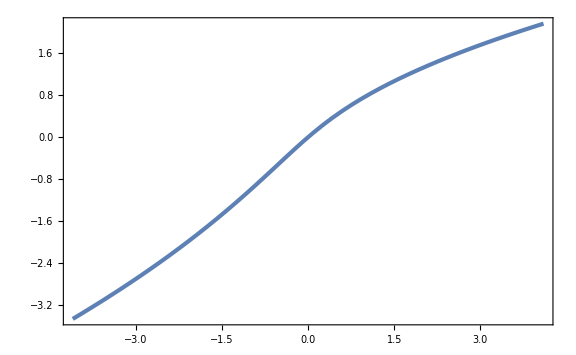

```mathematica
Plot[mu2int[fNL]fNL,{fNL,-4.1,4.1},GridLines->{None,{-5/6}}]
```

```mathematica
xmList=Table[{mufNL,x/.FindRoot[rmcond[x,1,mufNL]==0,{x,3.7}]},{mufNL,-5,5,10^-2}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

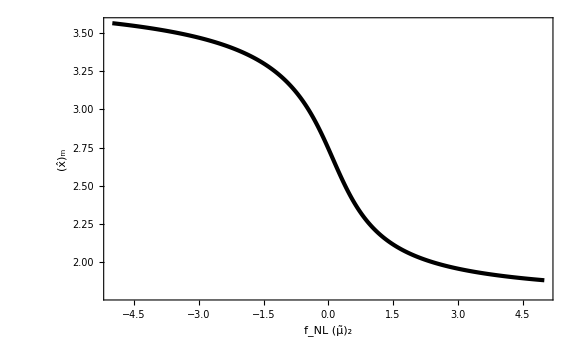

```mathematica
ListPlot[xmList,FrameLabel->{Subscript[OverTilde[μ], 2] Subscript[f, NL],Subscript[OverHat[x], "m"]},PlotStyle->{AbsoluteThickness[3],Black}]
```

```mathematica
xmint[mufNL_]=Interpolation[xmList][mufNL];
```

```mathematica
Cpp[x_,mu_,fNL_]=D[D[CompactC[x,mu,fNL], x], x]//Simplify
```

1/(75 x^6)4 (-10 (5 x^2+mu (x Cos[x]-Sin[x]) (5 x+6 fNL mu Sin[x]))^2+8 x (5 x^2+mu (x Cos[x]-Sin[x]) (5 x+6 fNL mu Sin[x])) (10 x+mu (5+6 fNL mu Cos[x]) (x Cos[x]-Sin[x])-mu x Sin[x] (5 x+6 fNL mu Sin[x]))-x^2 (10 x+mu (5+6 fNL mu Cos[x]) (x Cos[x]-Sin[x])-mu x Sin[x] (5 x+6 fNL mu Sin[x]))^2+x^2 (5 x^2-5 mu x Sin[x]-6 fNL mu^2 Sin[x]^2+mu x Cos[x] (5 x+6 fNL mu Sin[x])) (mu x Cos[x] (5 x+24 fNL mu Sin[x])+5 (-2+3 mu x Sin[x])))

```mathematica
qq[mu_,fNL_]=-(xmint[mu fNL]^2 Cpp[xmint[mu fNL],mu,fNL])/(4(1-3/2 CompactC[xmint[mu fNL],mu,fNL])CompactC[xmint[mu fNL],mu,fNL]);
```

```mathematica
Cq[x_,mu_,fNL_]=(CompactC[xmint[mu fNL],mu,fNL] x^2)/(xmint[mu fNL]^2 E^(2zetabar[xmint[mu fNL],mu,fNL]))Exp[1/qq[mu,fNL](1-(x/(xmint[mu fNL] E^zetabar[xmint[mu fNL],mu,fNL]))^(2qq[mu,fNL]))];
```

```mathematica
Cbarmq[mu_,fNL_]:=3/2 E^(1/qq[mu,fNL])qq[mu,fNL]^(-1+5/(2qq[mu,fNL]))(Gamma[5/(2qq[mu,fNL])]-Gamma[5/(2qq[mu,fNL]),1/qq[mu,fNL]])CompactC[xmint[mu fNL],mu,fNL]/;mu<mu2int[fNL]
Cbarmq[mu_,fNL_]:=None/;!(mu<mu2int[fNL])
```

```mathematica
CbarmqmaxData=ParallelTable[{fNL,FindMaximum[{Cbarmq[mu,fNL],10^-2≤mu≤mu2int[fNL]},{mu,1/4}]},{fNL,-4,4,1/100}];//AbsoluteTiming
```

{27.2278,Null}

```mathematica
CbarmqmaxList=Table[{CbarmqmaxData[[i,1]],CbarmqmaxData[[i,2,1]]},{i,Length[CbarmqmaxData]}];
muqmaxList=Table[{CbarmqmaxData[[i,1]],mu/.CbarmqmaxData[[i,2,2]]},{i,Length[CbarmqmaxData]}];
```

```mathematica
Export["Cbarmqmax.dat",CbarmqmaxList];
Export["muqmax.dat",muqmaxList];
```

```mathematica
CbarmqmaxList=Import["Cbarmqmax.dat"]//ToExpression;
muqmaxList=Import["muqmax.dat"]//ToExpression;
```

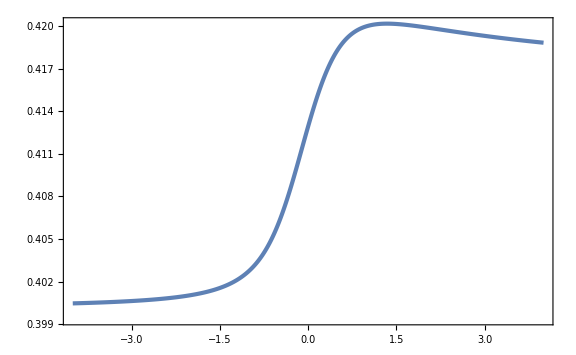

```mathematica
ListPlot[CbarmqmaxList]
```

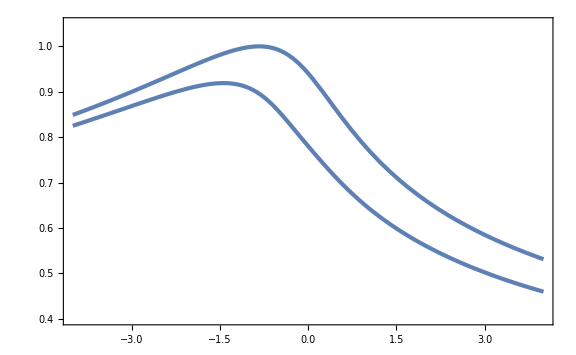

```mathematica
Show[ListPlot[muqmaxList,PlotRange->{0.4,1.05}],Plot[mu2int[fNL],{fNL,-4,4}]]
```

```mathematica
Cbarqmaxint[fNL_]=Interpolation[CbarmqmaxList][fNL];
```

```mathematica
Cbarqth=Cbarqmaxint[-125/100]
```

0.402021

```mathematica
muthqList=Table[{fNL,mu/.FindRoot[Cbarmq[mu,fNL]==2/5,{mu,1/4}]},{fNL,-4,4,1/100}];//AbsoluteTiming
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{11.7407,Null}

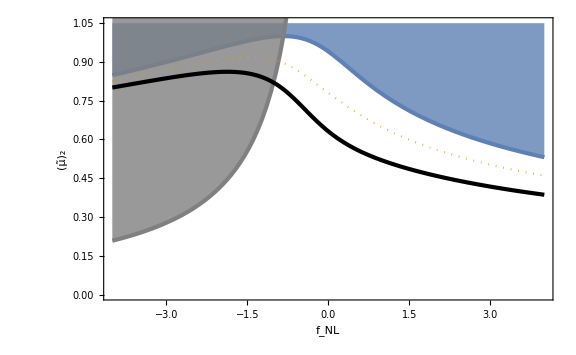

```mathematica
Show[Plot[mu2int[fNL],{fNL,-4,4},Filling->Top,FillingStyle->Opacity[0.8],PlotRange->{0,1.05},FrameLabel->{Subscript[f, NL],Subscript[OverTilde[μ], 2]}],Plot[-5/(6fNL),{fNL,-4,0},PlotStyle->{Gray,AbsoluteThickness[3]},Filling->Top,FillingStyle->Opacity[0.8]],ListPlot[{muthqList,muqmaxList},PlotStyle->{{Black,AbsoluteThickness[3]},Dotted}]]
```

```mathematica
muthqint[fNL_]=Interpolation[muthqList][fNL];
```

```mathematica
alpha[mu_,fNL_]=KK(mu-muthqint[fNL])^γ/.{KK->1,γ->0.36};
```

```mathematica
MoMks[mu_,fNL_]=xmint[mu fNL]^2 Exp[2zetabar[xmint[mu fNL],mu,fNL]]alpha[mu,fNL];
dLogMdmu[mu_,fNL_]=D[Log[MoMks[mu,fNL]], mu]//Simplify;
```

```mathematica
PlotMoMks[mu_,fNL_]:=MoMks[mu,fNL]/;(mu≥muthqint[fNL]&&mu≤mu2int[fNL])
PlotMoMks[mu_,fNL_]:=None/;(mu<muthqint[fNL]||mu>mu2int[fNL])
```

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
keq=0.07 0.143
```

0.01001

```mathematica
((10^20 gineV(3/(2π))^(3/2)(1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100 kminvsinvMpcineV)^2))^-1
```

5.28928×10^-16

```mathematica
PG[x_,sg2_]=1/(√(2π sg2))Exp[-x^2/(2sg2)];
```

```mathematica
fPBH[Mks_,ks_,As_,mu_,fNL_]=Mks/10^20 MoMks[mu,fNL](ks/(1.56 10^13))^3(f[mu/(√As)]PG[mu,As])/(5.3 10^-16)Abs[dLogMdmu[mu,fNL]]^-1 UnitStep[mu-muthqint[fNL]];
```

```mathematica
fPBHListfNLm1=Flatten[ParallelTable[{MoMks[muthqint[-1]+10^logmu,-1],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthqint[-1]+10^logmu,-1]//Quiet},{logmu,-10,Log10[mu2int[-1]-muthqint[-1]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHListfNL0=Flatten[ParallelTable[{MoMks[muthqint[0]+10^logmu,0],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthqint[0]+10^logmu,0]//Quiet},{logmu,-10,Log10[mu2int[0]-muthqint[0]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHListfNL1=Flatten[ParallelTable[{MoMks[muthqint[1]+10^logmu,1],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthqint[1]+10^logmu,1]//Quiet},{logmu,-10,Log10[mu2int[1]-muthqint[1]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHListfNL2=Flatten[ParallelTable[{MoMks[muthqint[2]+10^logmu,2],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthqint[2]+10^logmu,2]//Quiet},{logmu,-10,Log10[mu2int[2]-muthqint[2]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHListfNL3=Flatten[ParallelTable[{MoMks[muthqint[3]+10^logmu,3],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthqint[3]+10^logmu,3]//Quiet},{logmu,-10,Log10[mu2int[3]-muthqint[3]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHListfNL4=Flatten[ParallelTable[{MoMks[muthqint[4]+10^logmu,4],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthqint[4]+10^logmu,4]//Quiet},{logmu,-10,Log10[mu2int[4]-muthqint[4]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
```

{25.708,Null}

{29.0806,Null}

{26.3045,Null}

{25.4329,Null}

{26.7115,Null}

{25.9454,Null}

```mathematica
Export["fPBHqfNLm1.dat",fPBHListfNLm1];
Export["fPBHqfNL0.dat",fPBHListfNL0];
Export["fPBHqfNL1.dat",fPBHListfNL1];
Export["fPBHqfNL2.dat",fPBHListfNL2];
Export["fPBHqfNL3.dat",fPBHListfNL3];
Export["fPBHqfNL4.dat",fPBHListfNL4];
```

```mathematica
fPBHListfNLm1=Import["fPBHqfNLm1.dat"]//ToExpression;
fPBHListfNL0=Import["fPBHqfNL0.dat"]//ToExpression;
fPBHListfNL1=Import["fPBHqfNL1.dat"]//ToExpression;
fPBHListfNL2=Import["fPBHqfNL2.dat"]//ToExpression;
fPBHListfNL3=Import["fPBHqfNL3.dat"]//ToExpression;
fPBHListfNL4=Import["fPBHqfNL4.dat"]//ToExpression;
```

```mathematica
fPBHintfNLm1[M_,A_]=Interpolation[fPBHListfNLm1][M,A]UnitStep[MoMks[mu2int[-1],-1]-M,M-MoMks[muthqint[-1]+10^-10,-1]];
fPBHintfNL0[M_,A_]=Interpolation[fPBHListfNL0][M,A]UnitStep[MoMks[mu2int[0],0]-M,M-MoMks[muthqint[0]+10^-10,0]];
fPBHintfNL1[M_,A_]=Interpolation[fPBHListfNL1][M,A]UnitStep[MoMks[mu2int[1],1]-M,M-MoMks[muthqint[1]+10^-10,1]];
fPBHintfNL2[M_,A_]=Interpolation[fPBHListfNL2][M,A]UnitStep[MoMks[mu2int[2],2]-M,M-MoMks[muthqint[2]+10^-10,2]];
fPBHintfNL3[M_,A_]=Interpolation[fPBHListfNL3][M,A]UnitStep[MoMks[mu2int[3],3]-M,M-MoMks[muthqint[3]+10^-10,3]];
fPBHintfNL4[M_,A_]=Interpolation[fPBHListfNL4][M,A]UnitStep[MoMks[mu2int[4],4]-M,M-MoMks[muthqint[4]+10^-10,4]];
```

```mathematica
fPBHAListfNLm1=ParallelTable[{10^logA,NIntegrate[fPBHintfNLm1[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-3,0,10^-2}];//AbsoluteTiming
fPBHAListfNL0=ParallelTable[{10^logA,NIntegrate[fPBHintfNL0[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-3,0,10^-2}];//AbsoluteTiming
fPBHAListfNL1=ParallelTable[{10^logA,NIntegrate[fPBHintfNL1[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-3,0,10^-2}];//AbsoluteTiming
fPBHAListfNL2=ParallelTable[{10^logA,NIntegrate[fPBHintfNL2[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-7/2,0,10^-2}];//AbsoluteTiming
fPBHAListfNL3=ParallelTable[{10^logA,NIntegrate[fPBHintfNL3[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-7/2,0,10^-2}];//AbsoluteTiming
fPBHAListfNL4=ParallelTable[{10^logA,NIntegrate[fPBHintfNL4[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-7/2,0,10^-2}];//AbsoluteTiming
```

{5.12417,Null}

{5.31666,Null}

{6.15992,Null}

{6.30546,Null}

{6.08407,Null}

```mathematica
Export["fPBHAqfNLm1.dat",fPBHAListfNLm1];
Export["fPBHAqfNL0.dat",fPBHAListfNL0];
Export["fPBHAqfNL1.dat",fPBHAListfNL1];
Export["fPBHAqfNL2.dat",fPBHAListfNL2];
Export["fPBHAqfNL3.dat",fPBHAListfNL3];
Export["fPBHAqfNL4.dat",fPBHAListfNL4];
```

```mathematica
fPBHAListfNLm1=Import["fPBHAqfNLm1.dat"]//ToExpression;
fPBHAListfNL0=Import["fPBHAqfNL0.dat"]//ToExpression;
fPBHAListfNL1=Import["fPBHAqfNL1.dat"]//ToExpression;
fPBHAListfNL2=Import["fPBHAqfNL2.dat"]//ToExpression;
fPBHAListfNL3=Import["fPBHAqfNL3.dat"]//ToExpression;
fPBHAListfNL4=Import["fPBHAqfNL4.dat"]//ToExpression;
```

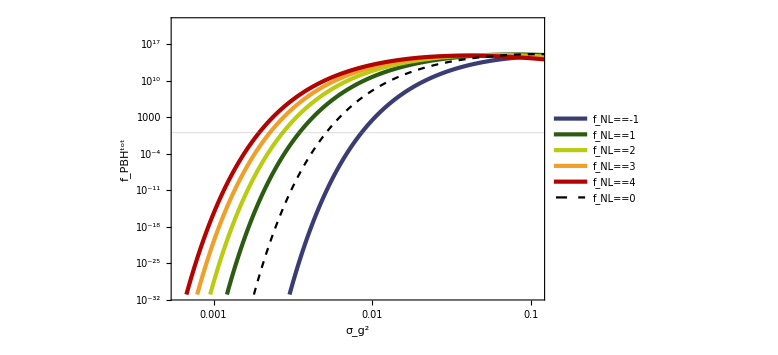

```mathematica
FigfPBHtotfNL=ListLogLogPlot[{fPBHAListfNLm1,fPBHAListfNL1,fPBHAListfNL2,fPBHAListfNL3,fPBHAListfNL4,fPBHAListfNL0},FrameLabel->{Subscript[σ, g]^2,Subscript[f, PBH]^tot},PlotRange->{{6 10^-4,1.1 10^-1},{10^-31,10^21}},GridLines->{None,{1}},PlotStyle->{{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[7]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[3]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]},{Black,Dashed}},PlotLegends->Placed[LineLegend[{Subscript[f, NL]==-1,Subscript[f, NL]==1,Subscript[f, NL]==2,Subscript[f, NL]==3,Subscript[f, NL]==4,Subscript[f, NL]==0},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->{"Column",2},LegendMarkerSize->20],{0.7,0.2}]]
```

```mathematica
Export["fPBHtotfNL.pdf",FigfPBHtotfNL];
```

```mathematica
fPBHAintfNLm1[A_]=Interpolation[fPBHAListfNLm1][A];
fPBHAintfNL0[A_]=Interpolation[fPBHAListfNL0][A];
fPBHAintfNL1[A_]=Interpolation[fPBHAListfNL1][A];
fPBHAintfNL2[A_]=Interpolation[fPBHAListfNL2][A];
fPBHAintfNL3[A_]=Interpolation[fPBHAListfNL3][A];
fPBHAintfNL4[A_]=Interpolation[fPBHAListfNL4][A];
```

```mathematica
A1fNLm1=A/.FindRoot[Log10[fPBHAintfNLm1[A]]==0,{A,0.005}]
A1fNL0=A/.FindRoot[Log10[fPBHAintfNL0[A]]==0,{A,0.005}]
A1fNL1=A/.FindRoot[Log10[fPBHAintfNL1[A]]==0,{A,0.003}]
A1fNL2=A/.FindRoot[Log10[fPBHAintfNL2[A]]==0,{A,0.003}]
A1fNL3=A/.FindRoot[Log10[fPBHAintfNL3[A]]==0,{A,0.003}]
A1fNL4=A/.FindRoot[Log10[fPBHAintfNL4[A]]==0,{A,0.003}]
```

0.0085586

0.00511925

0.00347123

0.00272836

0.00226253

0.00193664

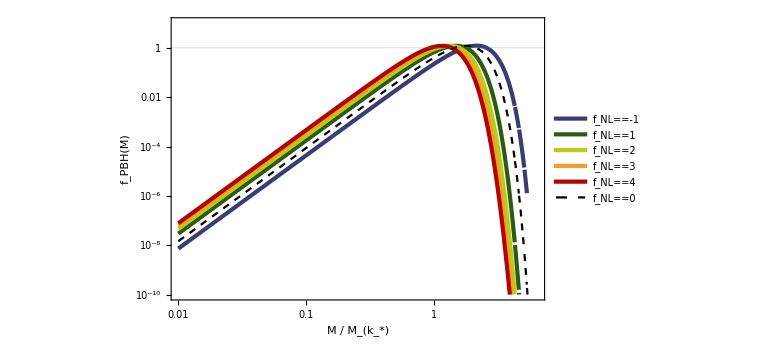

```mathematica
FigfPBHfNL=LogLogPlot[{fPBHintfNLm1[M,A1fNLm1],fPBHintfNL1[M,A1fNL1],fPBHintfNL2[M,A1fNL2],fPBHintfNL3[M,A1fNL3],fPBHintfNL4[M,A1fNL4],fPBHintfNL0[M,A1fNL0]},{M,0.01,10},GridLines->{None,{1}},FrameLabel->{Row[{M," / ",Subscript[M, SubStar[k]]}],Subscript[f, PBH][M]},PlotRange->{10^-10,10},PlotStyle->{{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[7]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[3]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]},{Black,Dashed}},PlotLegends->Placed[LineLegend[{Subscript[f, NL]==-1,Subscript[f, NL]==1,Subscript[f, NL]==2,Subscript[f, NL]==3,Subscript[f, NL]==4,Subscript[f, NL]==0},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->{"Column",2},LegendMarkerSize->20],{0.6,0.2}]]
```

```mathematica
Export["fPBHfNL.pdf",FigfPBHfNL];
```

### Press-Schechter

```mathematica
xm=2.74;
```

```mathematica
WRTH[z_]=3/z^3(Sin[z]-z Cos[z]);
```

```mathematica
sX[A_]=4/9 xm^2 WRTH[xm]Sqrt[A]
sY[A_,fNL_]=6/4 fNL Sinc[xm]Sqrt[A]
```

1.41746 √A

0.213988 √A fNL

```mathematica
PfNL[dl_,A_,fNL_]=1/Sqrt[2π sX[A]^2](Exp[(-((-sX[A]+Sqrt[sX[A]^2+4sX[A]sY[A,fNL]dl])/(2sY[A,fNL]))^2)/(2 sX[A]^2)]+Exp[(-((-sX[A]-Sqrt[sX[A]^2+4sX[A]sY[A,fNL]dl])/(2sY[A,fNL]))^2)/(2 sX[A]^2)])//Simplify
PGauss[dl_,A_]=1/Sqrt[2π sX[A]^2] Exp[Normal[Series[-((-sX[A]+Sqrt[sX[A]^2+4sX[A]sY[A,fNL]dl])/(2sY[A,fNL]))^2,{fNL,0,0}]]/(2 sX[A]^2)]//Simplify
```

(0.281448 (ⅇ^(-(1.35865 (-1.41746 √A+√(A (2.00921+1.21328 dl fNL)))^2)/(A^2 fNL^2))+ⅇ^(-(1.35865 (1.41746 √A+√(A (2.00921+1.21328 dl fNL)))^2)/(A^2 fNL^2))))/(√A)

(0.281448 ⅇ^(-(0.248855 dl^2)/A))/(√A)

General::munfl: Exp[-10658.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

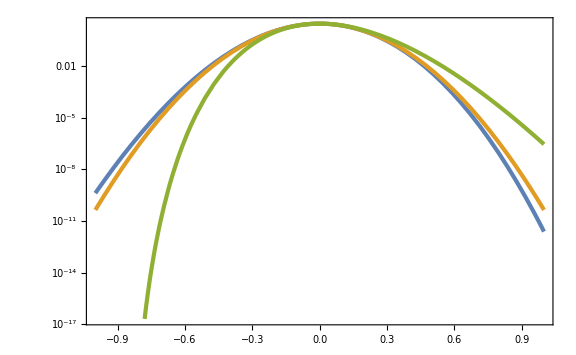

```mathematica
LogPlot[{PfNL[dl,10^-2,fNLmin],PGauss[dl,10^-2],PfNL[dl,10^-2,2]},{dl,-1,1}]
```

```mathematica
MoMksPS[dl_]=xm^2 KK(dl-3/8 dl^2-Cth)^γ/.{KK->1,γ->0.36,Cth->0.587}
β[dl_,A_,fNL_]=(KK(dl-3/8 dl^2-Cth)^(γ+1))/(γ(1-3/4 dl))PfNL[dl,A,fNL]/.{KK->1,γ->0.36,Cth->0.587}

βGauss[dl_,A_]=(KK(dl-3/8 dl^2-Cth)^(γ+1))/(γ(1-3/4 dl))PGauss[dl,A]/.{KK->1,γ->0.36,Cth->0.587}
fPBHPS[dl_,A_,fNL_]=β[dl,A,fNL]/(6.88 10^-16);
fPBHPSGauss[dl_,A_]=βGauss[dl,A]/(6.88 10^-16);
```

7.5076 (-0.587+dl-(3 dl^2)/8)^0.36

(0.7818 (-0.587+dl-(3 dl^2)/8)^1.36 (ⅇ^(-(1.35865 (-1.41746 √A+√(A (2.00921+1.21328 dl fNL)))^2)/(A^2 fNL^2))+ⅇ^(-(1.35865 (1.41746 √A+√(A (2.00921+1.21328 dl fNL)))^2)/(A^2 fNL^2))))/(√A (1-(3 dl)/4))

(0.7818 (-0.587+dl-(3 dl^2)/8)^1.36 ⅇ^(-(0.248855 dl^2)/A))/(√A (1-(3 dl)/4))

```mathematica
dlth=4/3(1-Sqrt[1-3/2 Cth])/.{Cth->0.587}
dlmax=4/3;
```

0.872416

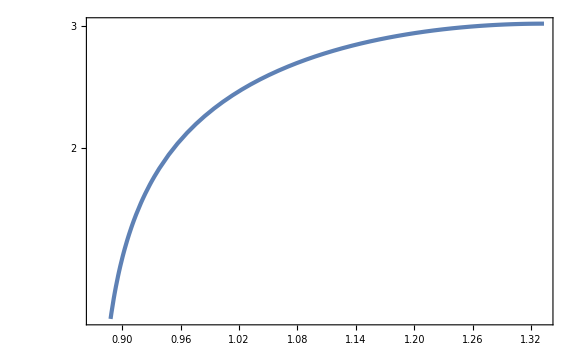

```mathematica
LogPlot[MoMksPS[dl],{dl,dlth,dlmax}]
```

```mathematica
fPBHPSListfNLmin=Flatten[ParallelTable[{MoMksPS[dlth+10^logdl],10^logA,fPBHPS[dlth+10^logdl,10^logA,fNLmin]//Quiet},{logdl,-10,Log10[dlmax-dlth],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHPSListfNL0=Flatten[ParallelTable[{MoMksPS[dlth+10^logdl],10^logA,fPBHPSGauss[dlth+10^logdl,10^logA]//Quiet},{logdl,-10,Log10[dlmax-dlth],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHPSListfNL2=Flatten[ParallelTable[{MoMksPS[dlth+10^logdl],10^logA,fPBHPS[dlth+10^logdl,10^logA,2]//Quiet},{logdl,-10,Log10[dlmax-dlth],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHPSListfNL4=Flatten[ParallelTable[{MoMksPS[dlth+10^logdl],10^logA,fPBHPS[dlth+10^logdl,10^logA,4]//Quiet},{logdl,-10,Log10[dlmax-dlth],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
```

{7.4048,Null}

{4.99572,Null}

{7.26934,Null}

{6.84714,Null}

```mathematica
Export["fPBHPSfNLmin.dat",fPBHPSListfNLmin];
Export["fPBHPSfNL0.dat",fPBHPSListfNL0];
Export["fPBHPSfNL2.dat",fPBHPSListfNL2];
Export["fPBHPSfNL4.dat",fPBHPSListfNL4];
```

```mathematica
fPBHPSListfNLmin=Import["fPBHPSfNLmin.dat"]//ToExpression;
fPBHPSListfNL0=Import["fPBHPSfNL0.dat"]//ToExpression;
fPBHPSListfNL2=Import["fPBHPSfNL2.dat"]//ToExpression;
fPBHPSListfNL4=Import["fPBHPSfNL4.dat"]//ToExpression;
```

```mathematica
Mmax=MoMksPS[dlmax]
Mmin=MoMksPS[dlth+10^-10]
```

3.01968

0.00128655

```mathematica
fPBHPSintfNLmin[M_,A_]=Interpolation[fPBHPSListfNLmin][M,A]UnitStep[Mmax-M,M-Mmin];
fPBHPSintfNL0[M_,A_]=Interpolation[fPBHPSListfNL0][M,A]UnitStep[Mmax-M,M-Mmin];
fPBHPSintfNL2[M_,A_]=Interpolation[fPBHPSListfNL2][M,A]UnitStep[Mmax-M,M-Mmin];
fPBHPSintfNL4[M_,A_]=Interpolation[fPBHPSListfNL4][M,A]UnitStep[Mmax-M,M-Mmin];
```

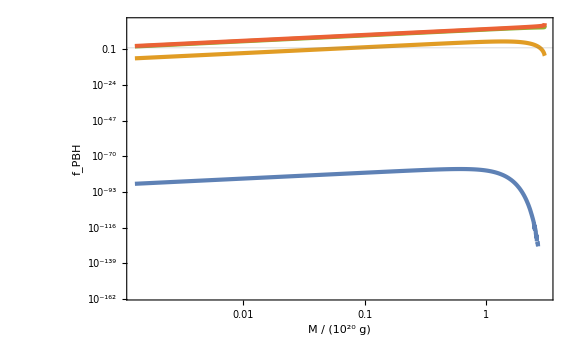

```mathematica
LogLogPlot[{fPBHPSintfNLmin[M,10^-3],fPBHPSintfNLmin[M,10^-2],fPBHPSintfNLmin[M,10^-1],fPBHPSintfNLmin[M,1]},{M,Mmin,Mmax},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

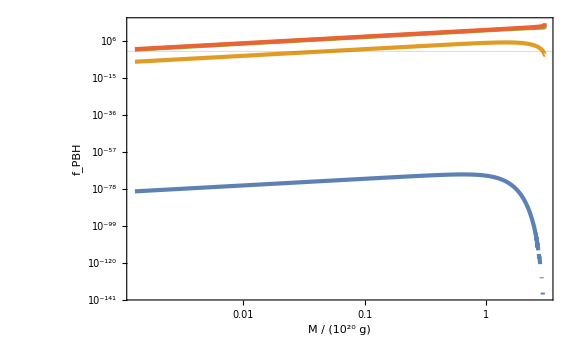

```mathematica
LogLogPlot[{fPBHPSintfNL0[M,10^-3],fPBHPSintfNL0[M,10^-2],fPBHPSintfNL0[M,10^-1],fPBHPSintfNL0[M,1]},{M,Mmin,Mmax},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

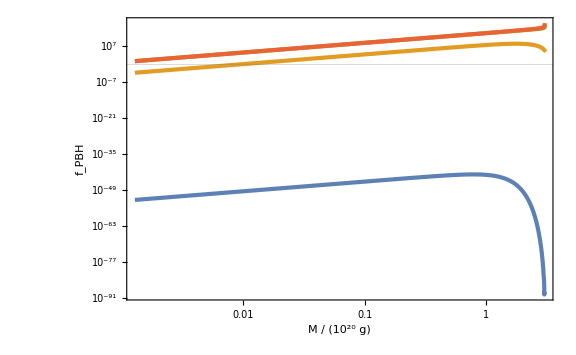

```mathematica
LogLogPlot[{fPBHPSintfNL2[M,10^-3],fPBHPSintfNL2[M,10^-2],fPBHPSintfNL2[M,10^-1],fPBHPSintfNL2[M,1]},{M,Mmin,Mmax},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

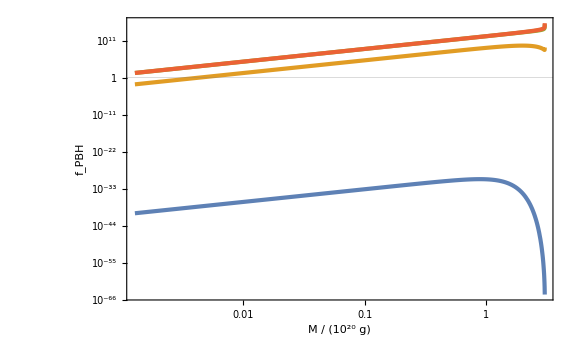

```mathematica
LogLogPlot[{fPBHPSintfNL4[M,10^-3],fPBHPSintfNL4[M,10^-2],fPBHPSintfNL4[M,10^-1],fPBHPSintfNL4[M,1]},{M,Mmin,Mmax},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

```mathematica
fPBHAPSListfNLmin=ParallelTable[{10^logA,NIntegrate[fPBHPSintfNLmin[E^logM,10^logA],{logM,Log[Mmin],Log[Mmax]}]//Quiet},{logA,-4,0,10^-2}];//AbsoluteTiming
fPBHAPSListfNL0=ParallelTable[{10^logA,NIntegrate[fPBHPSintfNL0[E^logM,10^logA],{logM,Log[Mmin],Log[Mmax]}]//Quiet},{logA,-4,0,10^-2}];//AbsoluteTiming
fPBHAPSListfNL2=ParallelTable[{10^logA,NIntegrate[fPBHPSintfNL2[E^logM,10^logA],{logM,Log[Mmin],Log[Mmax]}]//Quiet},{logA,-4,0,10^-2}];//AbsoluteTiming
fPBHAPSListfNL4=ParallelTable[{10^logA,NIntegrate[fPBHPSintfNL4[E^logM,10^logA],{logM,Log[Mmin],Log[Mmax]}]//Quiet},{logA,-4,0,10^-2}];//AbsoluteTiming
```

{9.9394,Null}

{9.95662,Null}

{9.94781,Null}

{10.1006,Null}

```mathematica
Export["fPBHAPSfNLmin.dat",fPBHAPSListfNLmin];
Export["fPBHAPSfNL0.dat",fPBHAPSListfNL0];
Export["fPBHAPSfNL2.dat",fPBHAPSListfNL2];
Export["fPBHAPSfNL4.dat",fPBHAPSListfNL4];
```

```mathematica
fPBHAPSListfNLmin=Import["fPBHAPSfNLmin.dat"]//ToExpression;
fPBHAPSListfNL0=Import["fPBHAPSfNL0.dat"]//ToExpression;
fPBHAPSListfNL2=Import["fPBHAPSfNL2.dat"]//ToExpression;
fPBHAPSListfNL4=Import["fPBHAPSfNL4.dat"]//ToExpression;
```

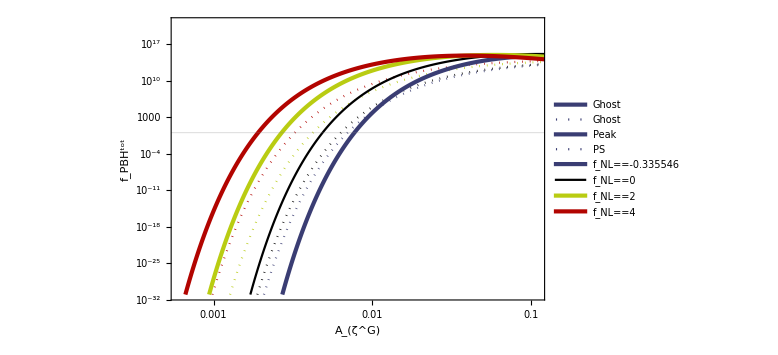

```mathematica
Show[ListLogLogPlot[{fPBHAPSListfNLmin,fPBHAPSListfNL0,fPBHAPSListfNL2,fPBHAPSListfNL4,fPBHAListfNLmin,fPBHAListfNL0,fPBHAListfNL2,fPBHAListfNL4},FrameLabel->{Subscript[A, ζ^("G")],Subscript[f, PBH]^tot},PlotRange->{{6 10^-4,1.1 10^-1},{10^-31,10^21}},GridLines->{None,{1}},PlotStyle->{{ColorData[10,"ColorList"][[9]],Dotted},{Black,Dotted},{ColorData[10,"ColorList"][[5]],Dotted},{ColorData[10,"ColorList"][[1]],Dotted},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Black},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]}}],
LogLogPlot[{0,0,0,0,0,0,0,0},{x,0.1,1},PlotStyle->{{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Dotted,ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Dotted,ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Black},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]}},PlotLegends->Placed[LineLegend[{"Ghost","Ghost","Peak","PS",Subscript[f, NL]==fNLmin,Subscript[f, NL]==0,Subscript[f, NL]==2,Subscript[f, NL]==4},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->20,LegendLayout->{"Column",2}],{0.75,0.25}]]]
```

```mathematica
fPBHAPSintfNLmin[A_]=Interpolation[fPBHAPSListfNLmin][A];
fPBHAPSintfNL0[A_]=Interpolation[fPBHAPSListfNL0][A];
fPBHAPSintfNL2[A_]=Interpolation[fPBHAPSListfNL2][A];
fPBHAPSintfNL4[A_]=Interpolation[fPBHAPSListfNL4][A];
```

```mathematica
A1PSfNLmin=A/.FindRoot[Log10[fPBHAPSintfNLmin[A]]==0,{A,0.003}]
A1PSfNL0=A/.FindRoot[Log10[fPBHAPSintfNL0[A]]==0,{A,0.003}]
A1PSfNL2=A/.FindRoot[Log10[fPBHAPSintfNL2[A]]==0,{A,0.003}]
A1PSfNL4=A/.FindRoot[Log10[fPBHAPSintfNL4[A]]==0,{A,0.003}]
```

0.00699411

0.00633633

0.00422324

0.00325043

InterpolatingFunction::dmval: Input value {0.000100024,0.00699411} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000126515,0.00699411} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000160024,0.00699411} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

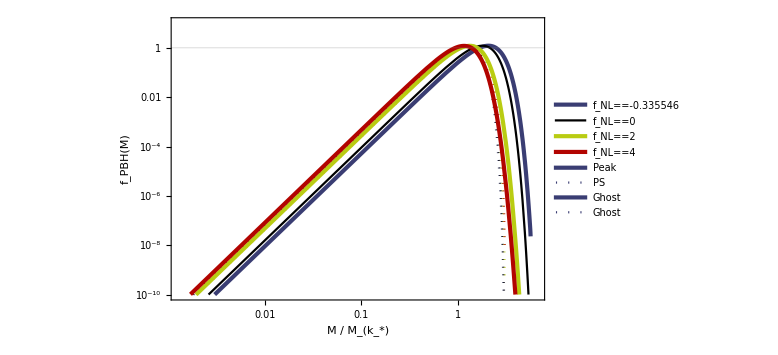

```mathematica
Show[LogLogPlot[{fPBHPSintfNLmin[M,A1PSfNLmin],fPBHPSintfNL0[M,A1PSfNL0],fPBHPSintfNL2[M,A1PSfNL2],fPBHPSintfNL4[M,A1PSfNL4],fPBHintfNLmin[M,A1fNLmin],fPBHintfNL0[M,A1fNL0],fPBHintfNL2[M,A1fNL2],fPBHintfNL4[M,A1fNL4]},{M,10^-4,10},GridLines->{None,{1}},FrameLabel->{Row[{M," / ",Subscript[M, SubStar[k]]}],Subscript[f, PBH][M]},PlotRange->{10^-10,10},PlotStyle->{{ColorData[10,"ColorList"][[9]],Dotted},{Black,Dotted},{ColorData[10,"ColorList"][[5]],Dotted},{ColorData[10,"ColorList"][[1]],Dotted},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Black},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]}}],
LogLogPlot[{0,0,0,0,0,0,0,0},{x,0.1,1},PlotStyle->{{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Black},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Dotted,ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Dotted,ColorData[10,"ColorList"][[9]]}},PlotLegends->Placed[LineLegend[{Subscript[f, NL]==fNLmin,Subscript[f, NL]==0,Subscript[f, NL]==2,Subscript[f, NL]==4,"Peak","PS","Ghost","Ghost"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->20,LegendLayout->{"Column",2}],{0.3,0.65}]]]
```